```mathematica
Ra = p2 M[x] + p3 M0 + p4 M0; (*compatible pollens for Ha *)
Rb = p1 M[x] + p3 M0 + p4 M0;
```

```mathematica
Ra1 = p2[t]M[x] + p3[t] M0 + p4[t] M0; (*compatible pollens for Ha *)
Rb1 = p1[t] M[x] + p3[t] M0 + p4[t] M0;
```

```mathematica
w11 = F[xm] 1/2(1/2 p2 M[x] + 1/2 p3 M0 + 1/4 p4 M0)/Ra + p2 F[x] 1/2 (1/2 M[xm])/Rb;
w12 = F[xm] 1/2(1/2 p1 M[x] + 1/2 p3 M0 (1-δ)/2)/Rb + p1 F[x] 1/2 (1/2 M[xm])/Ra;
w13 =p1 F[x] 1/2 (1/2 M0)/Ra + p2 F[x] 1/2 (1/2 M0 (1-δ)/2)/Rb;
w14 =p1 F[x] 1/2 (1/4 M0)/Ra;
w21 = F[xm] 1/2(1/2 p2 M[x] +  1/4 p4 M0)/Ra + p2 F[x] 1/2 (1/2 M[xm])/Rb;
w22 = F[xm] 1/2(1/2 p1 M[x] + 1/2 p3 M0 (1-δ)/2 + p4 M0 (1-δ)/2)/Rb + p1 F[x] 1/2 (1/2 M[xm])/Ra;
w23 = p2 F[x] 1/2 (1/2 M0 (1-δ)/2)/Rb;
w24 = p1 F[x] 1/2 (1/4 M0)/Ra + p2 F[x] 1/2 (M0 (1-δ)/2)/Rb;
w31 = F[xm] 1/2(1/2 p3 M0 + 1/4 p4 M0)/Ra;
w32 = F[xm] 1/2(1/2 p3 M0 (1+δ)/2)/Rb;
w33 =  p1 F[x] 1/2 (1/2 M0)/Ra + p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w34 = p1 F[x] 1/2 (1/4 M0)/Ra;
w41 =  F[xm] 1/2(1/4 p4 M0)/Ra;
w42 = F[xm] 1/2(1/2 p3 M0 (1+δ)/2 +  p4 M0 (1+δ)/2)/Rb;
w43 =  p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w44 =  p1 F[x] 1/2 (1/4 M0)/Ra + p2 F[x] 1/2 (M0 (1+δ)/2)/Rb;
```

```mathematica
W = 1/(F[x](p1 + p2)){{w11,w12,w13,w14},{w21,w22,w23,w24},{w31,w32,w33,w34},{w41,w42,w43,w44}};(*Invasion matrix; *)
```

```mathematica
Wneut = W/.xm->x;
```

```mathematica
func={M -> Function[x, M0 (1-x)^a],F -> Function[x, F0 x^b]}; 
sum1 = {p2->1-p1-p3-p4};
```

```mathematica
p1[t+1]=.
p2[t+1]=.
p3[t+1]=.
p4[t+1]=.
```

Unset::norep: Assignment on p1 for p1[1+t] not found.

$Failed

```mathematica
(*finding eqm frequencies {p and Qneut}*)
```

```mathematica
Clear[simulateFrequencies]
```

```mathematica
simulateFrequencies[xVal_,nparRule_,plotResults_:True] := 
(
npar=nparRule;
x = xVal;
recurrenceRelations={
p1[t+1] == (p1[t] F[x](1/2 p2[t] M[x]+1/2 p3[t] M0 +1/4 p4[t] M0)/Ra1+p2[t] F[x](1/2 p1[t] M[x]+(1-δ)/4 p3[t] M0)/Rb1 )1/(F[x](p1[t] + p2[t]))/.p2[t]->1-p1[t]-p3[t]-p4[t]/.func/.npar/.x->xVal,
p2[t+1] == (p1[t] F[x](1/2 p2[t] M[x]+1/4 p4[t] M0)/Ra1+p2[t] F[x](1/2 p1[t] M[x]+(1-δ)/4 p3[t] M0 +(1-δ)/2 p4[t] M0)/Rb1 )1/(F[x](p1[t] + p2[t]))/.p2[t]->1-p1[t]-p3[t]-p4[t]/.func/.npar/.x->xVal,
p3[t+1] == (p1[t] F[x] 1/2(p3[t] M0 + 1/2 p4[t] M0)/Ra1+p2[t] F[x](1+δ)/2(1/2 p3[t] M0)/Rb1 )1/(F[x](p1[t] + p2[t]))/.p2[t]->1-p1[t]-p3[t]-p4[t]/.func/.npar/.x->xVal,
p4[t+1] ==(p1[t] F[x] 1/2(1/2 p4[t] M0)/Ra1+p2[t] F[x](1+δ)/2(1/2 p3[t] M0 +p4[t] M0)/Rb1 )1/(F[x](p1[t] + p2[t]))/.p2[t]->1-p1[t]-p3[t]-p4[t]/.func/.npar/.x->xVal
};
initialConditions={p1[0]==0.25,p2[0]==0.25,p3[0]==0.25,p4[0]==0.25};
numGenerations=100;
(*Simulate the recurrence table*)result=RecurrenceTable[Join[recurrenceRelations,initialConditions],{p1,p2,p3,p4},{t,0,numGenerations}];
p1Results=result[[All,1]];
    p2Results=result[[All,2]];
   p3Results=result[[All,3]];
   p4Results=result[[All,4]];
   generations=Range[0,numGenerations];
If[plotResults,Print[ListLinePlot[{p1Results,p2Results,p3Results,p4Results},PlotLegends->{"p1","p2","p3","p4"},AxesLabel->{"Generations","Frequencies"},PlotLabel->"Frequency Simulation over Generations",GridLines->Automatic]]];
(*Return the last generation frequencies*)
lastGenFrequencies={p1Results[[-1]],p2Results[[-1]],p3Results[[-1]],p4Results[[-1]]};
Return[lastGenFrequencies];
);
```

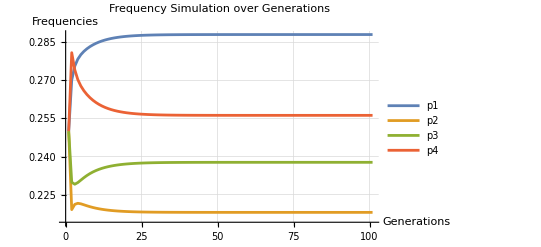

{0.288079,0.217982,0.237714,0.256226}

```mathematica
test = simulateFrequencies[0.8,{a->0.5,b->0.5,δ-> 0.5, M0->1,F0->1},True]
```

```mathematica
a=.
```

```mathematica
x=.
```

```mathematica
testmat1 = W/.sum1/.func/.p1->test[[1]]/.p3->test[[3]]/.p4->test[[4]]/.{a->0.5,b->0.5,δ-> 0.5, M0->1,F0->1}//Simplify//N
```

{{(0.373806 (1.-1. xm)^0.5)/(1.7146+1. (1.-1. x)^0.5)+((0.829073+0.494012 (1.-1. x)^0.5) xm^0.5)/((2.26597+1. (1.-1. x)^0.5) x^0.5),(0.652874 (1.-1. xm)^0.5)/(2.26597+1. (1.-1. x)^0.5)+((0.101911+0.494012 (1.-1. x)^0.5) xm^0.5)/((1.7146+1. (1.-1. x)^0.5) x^0.5),(1.33117+0.746325 (1.-1. x)^0.5)/(3.88523+3.98057 (1.-1. x)^0.5+1. (1.-1. x)^1.),0.326437/(2.26597+1. (1.-1. x)^0.5)},{(0.373806 (1.-1. xm)^0.5)/(1.7146+1. (1.-1. x)^0.5)+((0.290343+0.494012 (1.-1. x)^0.5) xm^0.5)/((2.26597+1. (1.-1. x)^0.5) x^0.5),(0.652874 (1.-1. xm)^0.5)/(2.26597+1. (1.-1. x)^0.5)+((0.321605+0.494012 (1.-1. x)^0.5) xm^0.5)/((1.7146+1. (1.-1. x)^0.5) x^0.5),0.0934514/(1.7146+1. (1.-1. x)^0.5),(0.983224+0.51334 (1.-1. x)^0.5)/(3.88523+3.98057 (1.-1. x)^0.5+1. (1.-1. x)^1.)},{(0.829073 xm^0.5)/((2.26597+1. (1.-1. x)^0.5) x^0.5),(0.305732 xm^0.5)/((1.7146+1. (1.-1. x)^0.5) x^0.5),(1.75469+0.933228 (1.-1. x)^0.5)/(3.88523+3.98057 (1.-1. x)^0.5+1. (1.-1. x)^1.),0.326437/(2.26597+1. (1.-1. x)^0.5)},{(0.290343 xm^0.5)/((2.26597+1. (1.-1. x)^0.5) x^0.5),(0.964816 xm^0.5)/((1.7146+1. (1.-1. x)^0.5) x^0.5),0.280354/(1.7146+1. (1.-1. x)^0.5),(1.83026+0.887146 (1.-1. x)^0.5)/(3.88523+3.98057 (1.-1. x)^0.5+1. (1.-1. x)^1.)}}

```mathematica
(D[LeadingEigenvaluesAndVectors[Transpose[testmat1],1][[2]],xm])/.x->0.8/.xm->0.8//Simplify//N
```

$Aborted

```mathematica
Eigensystem[testmat1]
```

```mathematica
p1Results
```

{0.25,0.290909,0.309932,0.323284,0.33222,0.338401,0.342742,0.345839,0.348077,0.349714,0.350921,0.351818,0.352489,0.352994,0.353374,0.353662,0.353881,0.354047,0.354173,0.354269,0.354342,0.354398,0.35444,0.354473,0.354498,0.354517,0.354531,0.354542,0.354551,0.354557,0.354562,0.354566,0.354569,0.354571,0.354572,0.354574,0.354575,0.354575,0.354576,0.354576,0.354577,0.354577,0.354577,0.354577,0.354577,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578,0.354578}

{a→1,b→1,δ→1,M0→1,F0→1}

```mathematica
(*sanity check and calculating V*)
```

```mathematica
P = {p1,p2,p3,p4}
```

{p1,p2,p3,p4}

```mathematica
LeadingEigenvaluesAndVectors[matrix_,k_]:=Module[
{eigenvalues,eigenvectors,sortedIndices,leadingEigenvalues,leadingEigenvectors},
(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[N[matrix,20]];
(*Sort the eigenvalues in descending order and get the indices*)
sortedIndices=Ordering[eigenvalues,-k];
(*Select the leading k eigenvalues and their corresponding eigenvectors*)
leadingEigenvalues=eigenvalues[[sortedIndices]][[1]];
leadingEigenvectors=eigenvectors[[sortedIndices]][[1]];
(*Return the leading eigenvalues and eigenvectors*)
{leadingEigenvalues,Re/@leadingEigenvectors}];
```

```mathematica
npar = {a->1.2,b->1,δ-> 1, M0->1,F0->1};
P = simulateFrequencies[0.5,npar,False];
mat = Wneut/.func/.x->0.5/.npar/.sum1/.p1->P[[1]]/.p3->P[[3]]/.p4->P[[4]]//Simplify;
V = LeadingEigenvaluesAndVectors[mat,1]
```

{1.,{0.604369,0.245875,0.615718,0.441786}}

```mathematica
V
```

{0.609541,0.384262,0.721498,1.5273}

```mathematica
Qneut = P
```

{0.143782,0.0962323,0.178105,0.489017}

```mathematica
k = V.Qneut
```

0.54454

```mathematica
V = V/k;
V.Qneut
```

1.

```mathematica
V
```

{0.609541,0.384262,0.721498,1.5273}

```mathematica
(*selgrad *)
```

```mathematica
selgrad =  V.(D[W,xm]/.xm->x/.x->0.7).Qneut/.sum1/.func/.npar/.p1->P[[1]]/.p3->P[[3]]/.p4->P[[4]]//Simplify
```

0.47026

```mathematica
(*sing value*)
```

```mathematica
singvalue[xVal_,eps_,tol_,nparRule_]:= (
npar=nparRule;
x = xVal;
maxIter=10;  (*Maximum number of iterations to prevent infinite loop*)
      iter=0;
While[True,
(*Increment iteration count*)
iter++;
P = simulateFrequencies[x,npar,True] ;
Qneut = P;
mat = Wneut/.func/.x->x/.npar/.sum1/.p1->P[[1]]/.p3->P[[3]]/.p4->P[[4]]//Simplify;
V = LeadingEigenvaluesAndVectors[mat,1][[2]];
k = V.Qneut;
V = V/k;
selgrad =  V.(D[W,xm]/.xm->x/.x->x).Qneut/.sum1/.func/.npar/.p1->P[[1]]/.p3->P[[3]]/.p4->P[[4]]//Simplify;
xNew=x+eps selgrad;
If[xNew<0||xNew>1,
Print["x went out of bounds: ",xNew];
Return[xNew]
];
If[Abs[xNew-x]<tol,
Return[xNew]
];
x=xNew;
Print[x]
If[iter>=maxIter,Print["Maximum iterations reached without convergence."];
Return[xNew]
];
]
)
```

```mathematica
npar = {a->0.7,b->0.7,δ->0,M0->1,F0->1}
```

{a→0.7,b→0.7,δ→0,M0→1,F0→1}

```mathematica
singvalue[0.4,0.01,10^-6,npar]
```

1.00288

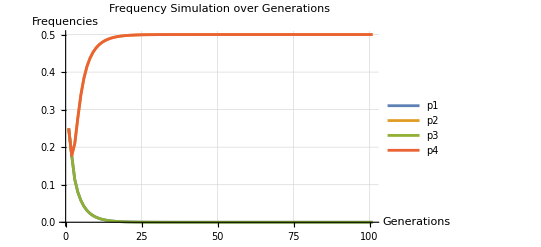

{1.05883×10^-12,0.5,1.05883×10^-12,0.5}

```mathematica
simulateFrequencies[1,npar,True]
```

```mathematica
npar={a->1,b->1,δ-> 1, M0->1,F0->1};
```

```mathematica
NumberForm[{1.23,1.2,1.54},2] (*use to simplify calculations*)
```

{1.2,1.2,1.5}

```mathematica
P = {p1,p2,p3,p4};
```

```mathematica
Qneut = {0.35,0.25,0.22,0.18};
```

```mathematica
V = {v1,v2,v3,v4};
```

```mathematica
dotrel = Solve[V.Qneut == 1,v1][[1]]//Simplify;
```

```mathematica
eqns = V.Wneut - V/.func/.x->0.25/.npar/.p2->1-p1-p3-p4/.p1->Qneut[[1]]/.p3->Qneut[[3]]/.p4->Qneut[[4]]//Simplify
```

{-0.529239 v1+0.314733 v2+0.219858 v3+0.0638298 v4,0.351265 v1-0.648735 v2+0.138365 v3+0.36478 v4,0.248227 v1-0.59454 v3+0.157233 v4,0.124113 v1+0.124113 v2+0.124113 v3-0.561421 v4}

```mathematica
V[[1]]/.dotrel
```

2.85714-0.714286 v2-0.628571 v3-0.514286 v4

```mathematica
(*vars = {V[[1]],V[[2]],V[[3]],V[[4]]};*)
```

```mathematica
V
```

{v1,v2,v3,v4}

```mathematica
coeffs = CoefficientArrays[eqns,V][[2]];
consts = -CoefficientArrays[eqns,V][[1]];
```

```mathematica
NullSpace[coeffs]
```

{}

```mathematica
sol=LinearSolve[CoefficientArrays[eqns,V][[2]],-CoefficientArrays[eqns,V][[1]]]
```

{0.,0.,0.,0.}

```mathematica
(*Simulate 1 locus model*)
```

```mathematica
R = p M0+ (1-p)M[x];
R1 = p[t] M0+ (1-p[t])M[x];
w22 = (1-p)/2 F[x](1-s)(1+δ)/2 M0/R; (*Number of mutant male seeds produced by a mutant male parent *)
w12 = (1-p)/2 F[x](1-s)(1-δ)/2 M0/R; (*Number of mutant hermaphrodite seeds produced by a mutant male parent *)
w11 =F[xm](s(1-d)+(1-s)/2(((1-p)M[x])/R+(p M0)/R(1-δ)/2)) + (1-p)/2 F[x](1-s)M[xm]/R; (* Number of mutant hermaphrodite seeds produced by a mutant hermaphrodite parent *)
w21 = 1/2 F[xm](1-s)(1+δ)/2(p M0)/R; (* Number of mutant male seeds produced by a mutant hermaphrodite parent *)
W = 1/(F[x](1-p)(1-s d)){{w11,w12},{w21,w22}};  (*Invasion matrix; term in beginning is the recruitment probability {(# individuals)/(# seeds)} *)

Wneut=W/. xm-> x//Simplify ;(*neutrality -> xm = x*)
func={M -> Function[x, M0 (1-x)^a],F -> Function[x, F0 x^b]};
```

```mathematica
Clear[simFreq1locus]
```

```mathematica
Wneut
```

{{(M0 p (1-δ+s (3-4 d+δ))+4 (-1+p) (-1+d s) M[x])/(4 (-1+p) (-1+d s) (M0 p+M[x]-p M[x])),-(M0 (-1+s) (-1+δ))/(4 (-1+d s) (M0 p+M[x]-p M[x]))},{-(M0 p (-1+s) (1+δ))/(4 (-1+p) (-1+d s) (M0 p+M[x]-p M[x])),(M0 (-1+s) (1+δ))/(4 (-1+d s) (M0 p+M[x]-p M[x]))}}

```mathematica
simFreq1locus[xVal_,nparRule_,gensValue_,plotResults_:True] := Module[
{xvalue=xVal,npar=nparRule,numGenerations=gensValue,func,recurrenceRelations,initialConditions,result,generations,lastGenFrequencies},
func={M -> Function[x, M0 (1-x)^a],F -> Function[x, F0 x^b]}; 
(*Print["x = ",xvalue];*)
(*Print[ "npar = ",npar];*)
(*Print[ "numGenerations = ",numGenerations];*)
recurrenceRelations={
p[t+1] == (1-p[t])F[x](1-s)(1+δ)/2(p[t] M0)/R1 1/(F[x](1-p[t])(1-s d))/.func/.npar/.x->xvalue
};
initialConditions={p[0]== 0.5};
(*Simulate the recurrence table*)
result=RecurrenceTable[Join[recurrenceRelations,initialConditions],p,{t,0,numGenerations}]/.x->xvalue//Simplify//N;
       generations=Range[0,numGenerations];
If[plotResults,
Print[ListLinePlot[1-result,
PlotLegends->"1-p (Herma Frequency)",
AxesLabel->{"Generations","Frequencies"},
PlotLabel->StringForm["Herma x = ``",xvalue],
GridLines->Automatic]]];
(*Return the last generation frequencies*)
lastGenFrequencies=1-result[[-1]]//N;
 Return[lastGenFrequencies];
];
```

```mathematica
npar = {a->0.5,b->0.5,δ-> 0,s->0,d->0, M0->1,F0->1};
```

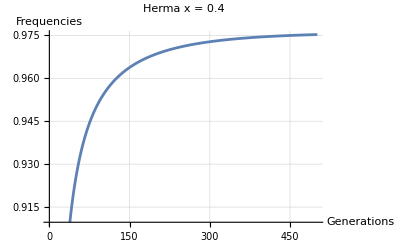

0.975301

```mathematica
simFreq1locus[0.4, {a->0.5,b->0.5,δ-> 0.56,s->0,d->0, M0->1,F0->1},500,True]
```

x = 0.55

npar = {a→0.5,b→0.5,δ→0.1,s→0,d→0,M0→1,F0→1}

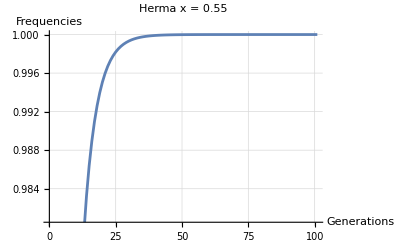

1.

```mathematica
npar = {a->0.5,b->0.5,δ-> 0.1,s->0,d->0, M0->1,F0->1};
hermfreq =  simFreq1locus[0.55,npar,100,True]
```

```mathematica
hermfreq
```

1.

```mathematica
1-hermfreq
```

5.02671×10^-10

```mathematica
mat
```

{{0.225,4.47609×10^8},{0.275,5.47077×10^8}}

```mathematica
Eigensystem[mat]
```

{{1.,0.409946},{{1.,3.49236×10^-10},{-0.494179,0.86936}}}

```mathematica
qneut = {hermfreq,1-hermfreq};
```

```mathematica
mat = Wneut/.func/.x->0.55/.npar/.p->1-hermfreq//Simplify;
```

```mathematica
mat = {{0.9984882801246998,0.3337723357707275},{0.004120646120626266,0.40794396594200033}}
```

{{0.998488,0.333772},{0.00412065,0.407944}}

```mathematica
mat
```

{{0.225,4.47609×10^8},{0.275,5.47077×10^8}}

```mathematica
Clear[LeadingEigenvaluesAndVectors]
```

```mathematica
LeadingEigenvaluesAndVectors[matrix_,k_]:=Module[
{eigenvalues,eigenvectors,sortedIndices,leadingEigenvalues,leadingEigenvectors},
(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[N[matrix,20]];
(*Sort the eigenvalues in descending order and get the indices*)
sortedIndices=Ordering[eigenvalues,-k];
(*Select the leading k eigenvalues and their corresponding eigenvectors*)
leadingEigenvalues=eigenvalues[[sortedIndices]][[1]]//N;
leadingEigenvectors=eigenvectors[[sortedIndices]][[1]]//N;
(*Return the leading eigenvalues and eigenvectors*)
{leadingEigenvalues,leadingEigenvectors}];
```

```mathematica
V = LeadingEigenvaluesAndVectors[mat,1][[2]]
```

{0.999976,0.00695024}

```mathematica
mat
```

{{0.227273,22.5},{0.277778,27.5}}

```mathematica
selgrad =  V.(D[W,xm]/.xm->0.99/.x->0.99).qneut/.func/.npar/.p->1-hermfreq//Simplify;
```

```mathematica
selgrad
```

-1.4285

```mathematica
W
```

{{(F[xm] ((1-d) s+1/2 (1-s) ((M0 p (1-δ))/(2 (M0 p+(1-p) M[x]))+((1-p) M[x])/(M0 p+(1-p) M[x])))+((1-p) (1-s) F[x] M[xm])/(2 (M0 p+(1-p) M[x])))/((1-p) (1-d s) F[x]),(M0 (1-s) (1-δ))/(4 (1-d s) (M0 p+(1-p) M[x]))},{(M0 p (1-s) (1+δ) F[xm])/(4 (1-p) (1-d s) F[x] (M0 p+(1-p) M[x])),(M0 (1-s) (1+δ))/(4 (1-d s) (M0 p+(1-p) M[x]))}}

```mathematica
mat = {{1,3},{4,2}}
```

{{1,3},{4,2}}

```mathematica
Eigensystem[mat]
```

{{5,-2},{{3,4},{-1,1}}}

```mathematica
v1 = {3,4}
```

{3,4}

```mathematica
mat.v1
```

{15,20}

```mathematica
Clear[CalculateHessian]
```

```mathematica
CalculateHessian[xsv_,npar_,Qneut_,V_]:=Module[
{xsvval=xsv,Q,DQ,Hessian,nparVal=npar,Qneutval=Qneut,Vval = V},
testmat = W/.func/.nparVal/.p->1-Qneut[[1]]//Simplify//N;
Q = LeadingEigenvaluesAndVectors[Transpose[testmat],1][[2]];
(*Print[StringForm["Q:``",Q]];*)
DQ = D[Q,xm]/.  xm->xsvval/. x->xsvval;
(*Print[StringForm["DQ:``",DQ]];*)
Hessian=Vval.(D[D[testmat,xm],xm]/. xm->xsvval/. x->xsvval).Qneutval+Vval.(D[testmat,xm]/. xm->xsvval/. x->xsvval).DQ;
Return[Hessian];
];
```

```mathematica
hessian
```

hessian

```mathematica
Clear[singvalue1locus]
```

```mathematica
singvalue1locus[xVal_,eps_,tol_,nparRule_,gensValue_,maxIterval_,printstat_:False]:=Module[
{xvalue=xVal,func,gens=gensValue,iter=0,hermfreq,qneut,mat,V,k,xAdj,selgrad,xNew,npar=nparRule,hessian},
func={M -> Function[x, M0 (1-x)^a],F -> Function[x, F0 x^b]}; 
While[True,
(*Increment iteration count*)
iter++;
Hessian
If[printstat,{Print[StringForm["Iter:``",iter]]}];


If[iter>maxIterval,
Print["Maximum iterations reached without convergence."];
hessian = CalculateHessian[xvalue,npar,qneut,V];
Return[{xvalue,qneut,hessian}]
];

(*Simulate frequencies;only plot on the last iteration*)
If[iter==maxIterval,
hermfreq=simFreq1locus[xvalue,npar,gens,True],
hermfreq=simFreq1locus[xvalue,npar,gens,False]];
If[printstat,Print[StringForm["hermfreq:``",hermfreq]]];

qneut = {hermfreq,1-hermfreq}//N;

(*Adjust qneut if it is {0,1} or {1,0}*)
If[qneut[[1]]>0.9999,
qneut={0.9999,0.0001}
];
       If[qneut[[1]]<0.01,
Print["Population collapse: no hermaphrodites left."];
Return[] ;
];
If[printstat,Print[StringForm["qneut:``",qneut]]];

mat = Wneut/.func/.x->xvalue/.npar/.p->qneut[[2]]//Simplify//N;
If[printstat,Print[StringForm["mat:``",mat]]];

V = LeadingEigenvaluesAndVectors[mat,1][[2]];
If[printstat,Print[StringForm["V:``",V]]];
k = V.qneut//N;
If[printstat,Print[StringForm["k:``",k]]];
V = If[k==0,V,V/k]//N;
(*Print[V];*)
If[printstat,Print[StringForm["V:``",V]]];

xAdj=If[xvalue==0,0.01,If[xvalue==1,0.99,xvalue]];
If[printstat,Print[StringForm["x after adjustment:``",xAdj]]];

selgrad =  V.(D[W,xm]/.xm->xAdj/.x->xAdj).qneut/.func/.npar/.p->qneut[[2]]//Simplify//N;
If[printstat,Print[StringForm["selgrad:``",selgrad]]];

xNew=xAdj+eps selgrad//N;
If[printstat,Print[StringForm["xNew:``",xNew]]];
If[xNew<0||xNew>1,
Print["x went out of bounds: ",xNew];
hessian = CalculateHessian[xNew,npar,qneut,V];
Return[{If[xNew<0,0,1],qneut,hessian}]
];
If[Abs[xNew-xvalue]<tol,
Print["Converged"];
hessian = CalculateHessian[xNew,npar,qneut,V];
Return[{xNew,qneut,hessian}]
];
xvalue=xNew;
If[printstat,Print[StringForm["x for new iteration:``",xvalue]]]
]
];
```

```mathematica
Null
```

```mathematica
W
```

{{(((1-p) (1-s) F[ComplexInfinity] M[xm])/(2 (M0 p+(1-p) M[ComplexInfinity]))+F[xm] ((1-d) s+1/2 (1-s) ((M0 p (1-δ))/(2 (M0 p+(1-p) M[ComplexInfinity]))+((1-p) M[ComplexInfinity])/(M0 p+(1-p) M[ComplexInfinity]))))/((1-p) (1-d s) F[ComplexInfinity]),(M0 (1-s) (1-δ))/(4 (1-d s) (M0 p+(1-p) M[ComplexInfinity]))},{(M0 p (1-s) (1+δ) F[xm])/(4 (1-p) (1-d s) F[ComplexInfinity] (M0 p+(1-p) M[ComplexInfinity])),(M0 (1-s) (1+δ))/(4 (1-d s) (M0 p+(1-p) M[ComplexInfinity]))}}

```mathematica
npar = {a->0.5,b->0.5,δ->0,s->0,d->0,M0->1,F0->1}
```

{a→0.5,b→0.5,δ→0,s→0,d→0,M0→1,F0→1}

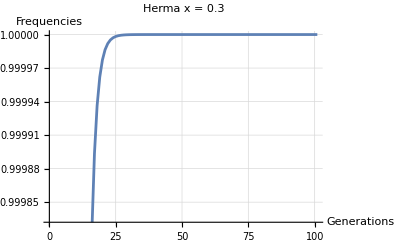

1.

```mathematica
hermfreq = simFreq1locus[0.3,npar,True]
```

```mathematica
hermfreq = 1;
```

```mathematica
qneut = {1-hermfreq,hermfreq}
```

{0,1}

```mathematica
mat = Wneut/.func/.x->0.3/.npar/.p->1-hermfreq//Simplify
```

{{1.,0.298807},{0.,0.298807}}

```mathematica
V = LeadingEigenvaluesAndVectors[mat,1][[2]]
```

{1.,0.}

```mathematica
V
```

{0.316228,0.948683}

```mathematica
k = V.qneut
```

1.

```mathematica
V = If[k==0,V,V/k]
```

{1.,3.49236×10^-10}

```mathematica
selgrad =  V.(D[W,xm]/.xm->x/.x->x).qneut/.func/.npar/.p->1-hermfreq//Simplify
```

-(0.25/(1-x)^0.5+(-5.65505×10^-11-0.25 (1-x)^0.5)/x^1.)/(5.02671×10^-10+1. (1-x)^0.5)

```mathematica
selgrad/.x->0.55//Simplify
```

-0.10101

0.

```mathematica
hermfreq
```

1.

```mathematica
npar
```

{a→0.5,b→0.5,δ→0,s→0,d→0,M0→1,F0→1}

```mathematica
singvalue1locus[0.4,10^-2,10^-9,{a->0.5,b->0.5,δ->0.5,s->0,d->0,M0->1,F0->1},200,3000]
```

Converged

{0.555555,{0.75,0.25},-0.91125}

```mathematica
Table[{StringForm["δ:``",δval],singvalue1locus[0.1,10^-2,10^-9,{a->0.5,b->0.5,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}]
```

Converged

Q:{-(0.00040404 (2525. √x-0.5 (2525. √x+√((-2525. √x-5000. √x √(1.-1. xm)-0.247525 √xm-5000. √(1.-1. x) √xm)^2-4. (1.2625×10^7 x √(1.-1. xm)+1.2625×10^7 √(1.-1. x) √x √xm))+5000. √x √(1.-1. xm)+0.247525 √xm+5000. √(1.-1. x) √xm)))/(√x),1.}

DQ:{0.0000558113,0}

Converged

Q:{-(0.000444444 (2750. √x-0.5 (2750. √x+√((-2750. √x-5000. √x √(1.-1. xm)-0.225023 √xm-5000. √(1.-1. x) √xm)^2-4. (1.375×10^7 x √(1.-1. xm)+1.375×10^7 √(1.-1. x) √x √xm))+5000. √x √(1.-1. xm)+0.225023 √xm+5000. √(1.-1. x) √xm)))/(√x),1.}

DQ:{0.0000639357,0}

Converged

Q:{-(0.0005 (3000. √x-0.5 (3000. √x+√((-3000. √x-5000. √x √(1.-1. xm)-0.20002 √xm-5000. √(1.-1. x) √xm)^2-4. (1.5×10^7 x √(1.-1. xm)+1.5×10^7 √(1.-1. x) √x √xm))+5000. √x √(1.-1. xm)+0.20002 √xm+5000. √(1.-1. x) √xm)))/(√x),1.}

DQ:{0.0000740191,0}

Converged

Q:{0.,0.}

DQ:{0,0}

$Aborted

```mathematica
(*quadrant 1*)
```

Converged

Converged

Converged

Eigensystem::eivec0: Unable to find all eigenvectors.

Converged

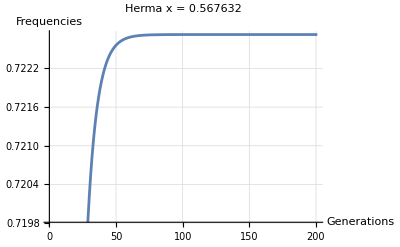

Maximum iterations reached without convergence.

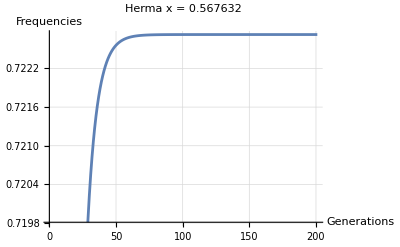

Maximum iterations reached without convergence.

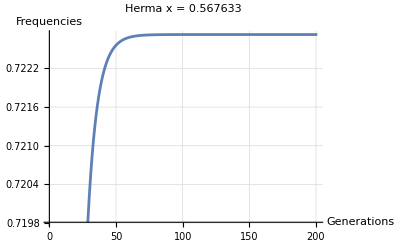

Maximum iterations reached without convergence.

Converged

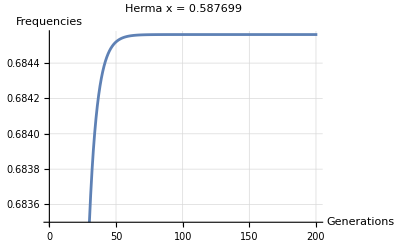

Maximum iterations reached without convergence.

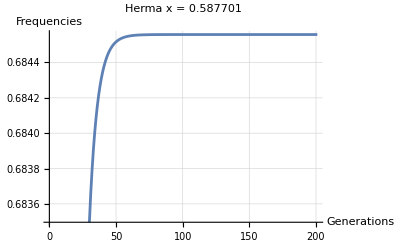

Maximum iterations reached without convergence.

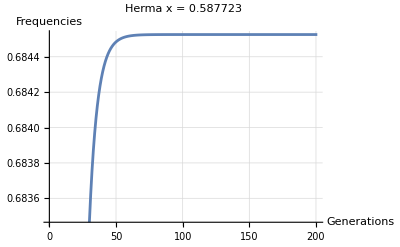

Maximum iterations reached without convergence.

Converged

Eigensystem::eivec0: Unable to find all eigenvectors.

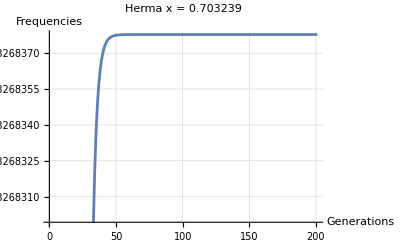

Maximum iterations reached without convergence.

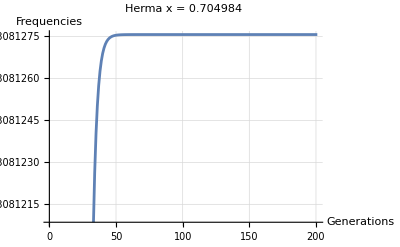

Maximum iterations reached without convergence.

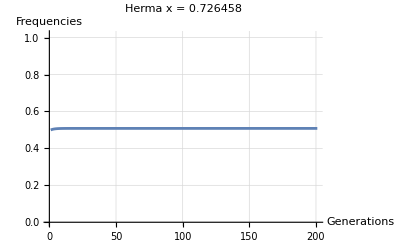

Maximum iterations reached without convergence.

Eigensystem::eivec0: Unable to find all eigenvectors.

General::stop: Further output of Eigensystem::eivec0 will be suppressed during this calculation.

Converged

Converged

Converged

«14 more identical outputs»

```mathematica
res12 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->0.5,b->0.5,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.5,0.505,0.51,0.515,0.52,0.54,0.55,0.6}}];
```

```mathematica
res2 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->2,b->0.5,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.4,0.5,0.7,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
```

Converged

Converged

Converged

«1 more identical outputs»

x went out of bounds: 1.0018

x went out of bounds: 1.00189

Converged

Converged

Converged

«1 more identical outputs»

x went out of bounds: 1.00019

x went out of bounds: 1.0015

Converged

Converged

Converged

x went out of bounds: 1.0012

x went out of bounds: 1.00056

x went out of bounds: 1.00199

x went out of bounds: 1.00009

x went out of bounds: 1.00063

x went out of bounds: 1.00221

x went out of bounds: 1.00053

x went out of bounds: 1.00139

x went out of bounds: 1.00089

x went out of bounds: 1.00159

x went out of bounds: 1.00219

x went out of bounds: 1.00217

x went out of bounds: 1.00137

x went out of bounds: 1.00041

x went out of bounds: 1.00128

x went out of bounds: 1.00138

x went out of bounds: 1.00002

x went out of bounds: 1.00064

x went out of bounds: 1.00176

x went out of bounds: 1.00119

x went out of bounds: 1.00239

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

«3 more identical outputs»

```mathematica
res3 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->2,b->2,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
```

x went out of bounds: 1.00978

x went out of bounds: 1.00623

x went out of bounds: 1.00349

x went out of bounds: 1.00052

x went out of bounds: 1.00117

x went out of bounds: 1.00762

x went out of bounds: 1.00057

x went out of bounds: 1.00182

x went out of bounds: 1.00695

x went out of bounds: 1.0034

x went out of bounds: 1.00275

x went out of bounds: 1.00296

x went out of bounds: 1.00578

x went out of bounds: 1.00139

x went out of bounds: 1.00996

x went out of bounds: 1.00444

x went out of bounds: 1.00277

x went out of bounds: 1.0065

x went out of bounds: 1.00265

x went out of bounds: 1.00518

x went out of bounds: 1.00515

x went out of bounds: 1.00637

x went out of bounds: 1.00747

x went out of bounds: 1.00548

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

«1 more identical outputs»

```mathematica
res4= Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->0.5,b->2,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
```

Converged

Converged

Eigensystem::eivec0: Unable to find all eigenvectors.

Converged

Converged

Converged

«8 more identical outputs»

Eigensystem::eivec0: Unable to find all eigenvectors.

Converged

Converged

Converged

x went out of bounds: 1.00178

x went out of bounds: 1.00247

Eigensystem::eivec0: Unable to find all eigenvectors.

General::stop: Further output of Eigensystem::eivec0 will be suppressed during this calculation.

x went out of bounds: 1.00001

x went out of bounds: 1.00337

x went out of bounds: 1.00055

x went out of bounds: 1.00174

x went out of bounds: 1.00714

x went out of bounds: 1.00269

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

«1 more identical outputs»

```mathematica
res42 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->0.5,b->1.5,δ->δval,s->0,d->0,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
```

Converged

Converged

Eigensystem::eivec0: Unable to find all eigenvectors.

Converged

Converged

Converged

«6 more identical outputs»

Eigensystem::eivec0: Unable to find all eigenvectors.

Converged

Converged

Converged

«2 more identical outputs»

x went out of bounds: 1.00091

Eigensystem::eivec0: Unable to find all eigenvectors.

General::stop: Further output of Eigensystem::eivec0 will be suppressed during this calculation.

x went out of bounds: 1.00012

x went out of bounds: 1.00057

x went out of bounds: 1.00055

x went out of bounds: 1.00038

x went out of bounds: 1.00156

x went out of bounds: 1.00292

x went out of bounds: 1.00544

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

Population collapse: no hermaphrodites left.

«1 more identical outputs»

```mathematica
res2
```

{{δ:0.01,{{x initial:0.1,{0.200012,{0.9999,0.0001}}},{x initial:0.25,{0.200012,{0.9999,0.0001}}},{x initial:0.4,{0.200012,{0.9999,0.0001}}},{x initial:0.5,{0.200012,{0.9999,0.0001}}},{x initial:0.7,{1,{0.495,0.505}}},{x initial:0.9,{1,{0.495,0.505}}}}},{δ:0.1,{{x initial:0.1,{0.200011,{0.9999,0.0001}}},{x initial:0.25,{0.200011,{0.9999,0.0001}}},{x initial:0.4,{0.200011,{0.9999,0.0001}}},{x initial:0.5,{0.200011,{0.9999,0.0001}}},{x initial:0.7,{1,{0.450002,0.549998}}},{x initial:0.9,{1,{0.45,0.55}}}}},{δ:0.2,{{x initial:0.1,{0.20001,{0.9999,0.0001}}},{x initial:0.25,{0.20001,{0.9999,0.0001}}},{x initial:0.4,{0.20001,{0.9999,0.0001}}},{x initial:0.5,{1,{0.400001,0.599999}}},{x initial:0.7,{1,{0.400002,0.599998}}},{x initial:0.9,{1,{0.4,0.6}}}}},{δ:0.4,{{x initial:0.1,{1,{0.300002,0.699998}}},{x initial:0.25,{1,{0.300001,0.699999}}},{x initial:0.4,{1,{0.3,0.7}}},{x initial:0.5,{1,{0.300001,0.699999}}},{x initial:0.7,{1,{0.3,0.7}}},{x initial:0.9,{1,{0.300001,0.699999}}}}},{δ:0.6,{{x initial:0.1,{1,{0.2,0.8}}},{x initial:0.25,{1,{0.2,0.8}}},{x initial:0.4,{1,{0.2,0.8}}},{x initial:0.5,{1,{0.2,0.8}}},{x initial:0.7,{1,{0.200001,0.799999}}},{x initial:0.9,{1,{0.2,0.8}}}}},{δ:0.8,{{x initial:0.1,{1,{0.1,0.9}}},{x initial:0.25,{1,{0.100001,0.899999}}},{x initial:0.4,{1,{0.1,0.9}}},{x initial:0.5,{1,{0.1,0.9}}},{x initial:0.7,{1,{0.1,0.9}}},{x initial:0.9,{1,{0.1,0.9}}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.4,Null},{x initial:0.5,Null},{x initial:0.7,Null},{x initial:0.9,Null}}}}

```mathematica
res3
```

{{δ:0.01,{{x initial:0.1,{1,{0.495,0.505}}},{x initial:0.25,{1,{0.495007,0.504993}}},{x initial:0.5,{1,{0.495021,0.504979}}},{x initial:0.9,{1,{0.495045,0.504955}}}}},{δ:0.1,{{x initial:0.1,{1,{0.450035,0.549965}}},{x initial:0.25,{1,{0.450003,0.549997}}},{x initial:0.5,{1,{0.45004,0.54996}}},{x initial:0.9,{1,{0.45003,0.54997}}}}},{δ:0.2,{{x initial:0.1,{1,{0.400004,0.599996}}},{x initial:0.25,{1,{0.400018,0.599982}}},{x initial:0.5,{1,{0.400021,0.599979}}},{x initial:0.9,{1,{0.40002,0.59998}}}}},{δ:0.4,{{x initial:0.1,{1,{0.300005,0.699995}}},{x initial:0.25,{1,{0.300023,0.699977}}},{x initial:0.5,{1,{0.3,0.7}}},{x initial:0.9,{1,{0.300009,0.699991}}}}},{δ:0.6,{{x initial:0.1,{1,{0.200011,0.799989}}},{x initial:0.25,{1,{0.200002,0.799998}}},{x initial:0.5,{1,{0.200011,0.799989}}},{x initial:0.9,{1,{0.200005,0.799995}}}}},{δ:0.8,{{x initial:0.1,{1,{0.100002,0.899998}}},{x initial:0.25,{1,{0.100001,0.899999}}},{x initial:0.5,{1,{0.100001,0.899999}}},{x initial:0.9,{1,{0.100002,0.899998}}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.5,Null},{x initial:0.9,Null}}}}

```mathematica
res42
```

{{δ:0.01,{{x initial:0.1,{0.75325,{0.982978,0.0170219}}},{x initial:0.25,{0.75325,{0.982978,0.0170219}}},{x initial:0.5,{0.75325,{0.982978,0.0170219}}},{x initial:0.9,{0.75325,{0.982978,0.017022}}}}},{δ:0.1,{{x initial:0.1,{0.78885,{0.832578,0.167422}}},{x initial:0.25,{0.78885,{0.832578,0.167422}}},{x initial:0.5,{0.78885,{0.832578,0.167422}}},{x initial:0.9,{0.78885,{0.832578,0.167422}}}}},{δ:0.2,{{x initial:0.1,{0.876701,{0.616466,0.383534}}},{x initial:0.25,{0.876701,{0.616466,0.383534}}},{x initial:0.5,{0.876701,{0.616466,0.383534}}},{x initial:0.9,{0.876701,{0.616466,0.383534}}}}},{δ:0.4,{{x initial:0.1,{0.991429,{0.330607,0.669393}}},{x initial:0.25,{0.991429,{0.330607,0.669393}}},{x initial:0.5,{0.991429,{0.330607,0.669393}}},{x initial:0.9,{0.991429,{0.330607,0.669393}}}}},{δ:0.6,{{x initial:0.1,{1,{0.208834,0.791166}}},{x initial:0.25,{1,{0.213562,0.786438}}},{x initial:0.5,{1,{0.212097,0.787903}}},{x initial:0.9,{1,{0.212178,0.787822}}}}},{δ:0.8,{{x initial:0.1,{1,{0.108894,0.891106}}},{x initial:0.25,{1,{0.107958,0.892042}}},{x initial:0.5,{1,{0.106746,0.893254}}},{x initial:0.9,{1,{0.102778,0.897222}}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.5,Null},{x initial:0.9,Null}}}}

```mathematica
res1[[6]][[2]][[1]][[2]][[2]][[1]]
```

0.102033

```mathematica
a = For[i=1,i<7,i++,res1[[i]][[2]][[1]][[2]][[1]]]
```

```mathematica
a
```

```mathematica
xsv = {};
 For[i=1,i<7,i++,xsv = Append[xsv,res1[[i]][[2]][[1]][[2]][[1]]]]
(*xsv = Append[xsv,1] (*for δ=0.999*)*)
xsv
```

{0.500017,0.500016,0.500014,0.500397,0.991632,1}

```mathematica
hfeq = {};
 For[i=1,i<7,i++,hfeq = Append[hfeq,res1[[i]][[2]][[1]][[2]][[2]][[1]]]]
(*hfeq= Append[hfeq,0.0005] (*for δ=0.999*)*)
hfeq
```

{0.9999,0.9999,0.9999,0.996298,0.220138,0.102033}

```mathematica
ListPlot[{xsv,hfeq},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}},PlotLegends->{"x^*","f_heq"}]
```

ListPlot::nonopt: Options expected (instead of {δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}) beyond position 1 in ListPlot[{{0.500017,0.500016,0.500014,0.500397,0.991632,1,1},{0.9999,0.9999,0.9999,0.996298,0.220138,0.102033,0}},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}},PlotLegends→{x^*,f_heq}]. An option must be a rule or a list of rules.

```mathematica
delta = {0.01,0.1,0.2,0.4,0.6,0.8}
```

{0.01,0.1,0.2,0.4,0.6,0.8}

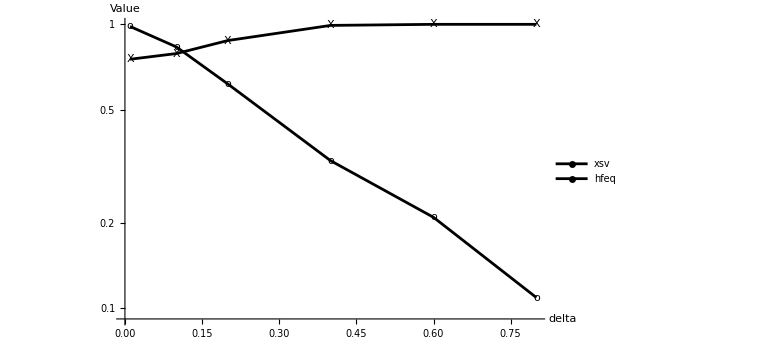

{0.500017,0.500016,0.500014,0.500397,0.991632,1}

{{δ:0.01,{{x initial:0.1,{0.75325,{0.982978,0.0170219},-1.35669}},{x initial:0.25,{0.75325,{0.982978,0.0170219},-1.35669}},{x initial:0.5,{0.75325,{0.982978,0.0170219},-1.35669}},{x initial:0.9,{0.75325,{0.982978,0.017022},-1.35669}}}},{δ:0.1,{{x initial:0.1,{0.78885,{0.832578,0.167422},-1.64875}},{x initial:0.25,{0.78885,{0.832578,0.167422},-1.64875}},{x initial:0.5,{0.78885,{0.832578,0.167422},-1.64875}},{x initial:0.9,{0.78885,{0.832578,0.167422},-1.64875}}}},{δ:0.2,{{x initial:0.1,{0.876701,{0.616466,0.383534},-2.98122}},{x initial:0.25,{0.876701,{0.616466,0.383534},-2.98122}},{x initial:0.5,{0.876701,{0.616466,0.383534},-2.98122}},{x initial:0.9,{0.876701,{0.616466,0.383534},-2.98123}}}},{δ:0.4,{{x initial:0.1,{0.991429,{0.330607,0.669393},-43.7503}},{x initial:0.25,{0.991429,{0.330607,0.669393},-43.7503}},{x initial:0.5,{0.991429,{0.330607,0.669393},-43.7503}},{x initial:0.9,{0.991429,{0.330607,0.669393},-43.7503}}}},{δ:0.6,{{x initial:0.1,{1,{0.208834,0.791166},-2.60043-373.496 ⅈ}},{x initial:0.25,{1,{0.213562,0.786438},-24.7376-8513.9 ⅈ}},{x initial:0.5,{1,{0.212097,0.787903},-4.68842-788.76 ⅈ}},{x initial:0.9,{1,{0.212178,0.787822},-212.625-633.218 ⅈ}}}},{δ:0.8,{{x initial:0.1,{1,{0.108894,0.891106},-172.204+590.252 ⅈ}},{x initial:0.25,{1,{0.107958,0.892042},0.220175-32.7095 ⅈ}},{x initial:0.5,{1,{0.106746,0.893254},0.29456-12.5026 ⅈ}},{x initial:0.9,{1,{0.102778,0.897222},59.8403+250.668 ⅈ}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.5,Null},{x initial:0.9,Null}}}}

```mathematica
(*Create a custom plot marker for "x"*)
(*xMarker=Graphics[{Thick,Line[{{-0.01,-0.01},{0.01,0.01}}],Line[{{-0.01,0.01},{0.01,-0.01}}]}];*)

(*Plot with logarithmic x-axis and normal y-axis*)
mainPlot = ListLogPlot[
{
Transpose[{delta,xsv}],
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black,Black},
PlotMarkers->{"X","o"},
PlotLegends->{"xsv","hfeq"},
AxesLabel->{"delta","Value"},
GridLines->Automatic,
PlotRange->All,
ImageSize->Large
]
(*additionalMarkerPlot=ListPlot[{{0.999,-2.4}},PlotStyle->{Red},PlotMarkers->"ex",PlotRange->All,PlotStyle->Directive[Red,PointSize[Large]]];
Show[mainPlot,additionalMarkerPlot]*)
```

```mathematica
hes = {}
For[i=1,i<7,i++,hes = Append[hes,Re[res1[[i]][[2]][[1]][[2]][[3]]]]]
```

{}

```mathematica
hes
```

{-0.999994,-0.99999,-0.999987,-0.999248,-15.1905,-0.74162}

```mathematica
Transpose[{delta,hfeq}]
```

{{0.01,0.9999},{0.1,0.9999},{0.2,0.9999},{0.4,0.996298},{0.6,0.220138},{0.8,0.102033}}

```mathematica
negativePoints
positivePoints
```

{{0.01,0.500017},{0.1,0.500016},{0.2,0.500014},{0.4,0.500397},{0.6,0.991632},{0.8,1}}

{}

{}

{-0.999994,-0.99999,-0.999987,-0.999248,-15.1905,-0.74162}

{{0.01,0.500017},{0.1,0.500016},{0.2,0.500014},{0.4,0.500397},{0.6,0.991632},{0.8,1}}

{}

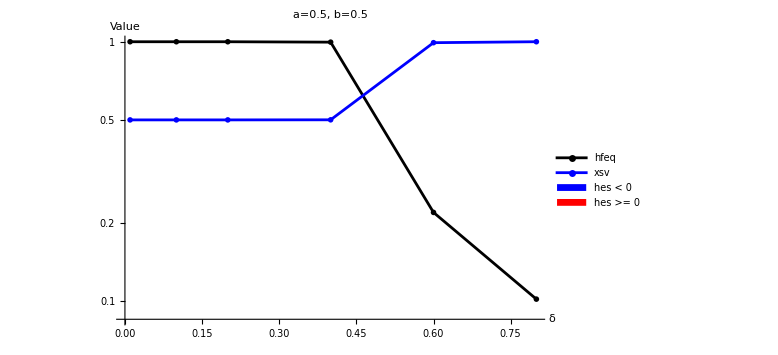

```mathematica
xsv = {};
For[i=1,i<7,i++,xsv = Append[xsv,res1[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<7,i++,hfeq = Append[hfeq,res1[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<7,i++,hes = Append[hes,Re[res1[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=0.5",18],
GridLines->Automatic,
PlotRange->All,
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

{0.200012,0.200011,0.20001,1,1,1}

{0.9999,0.9999,0.9999,0.300002,0.2,0.1}

{}

{-1.56222,-1.56224,-1.56226,1.06906,2.45209,11.1432}

{{0.01,0.200012},{0.1,0.200011},{0.2,0.20001}}

{{0.4,1},{0.6,1},{0.8,1}}

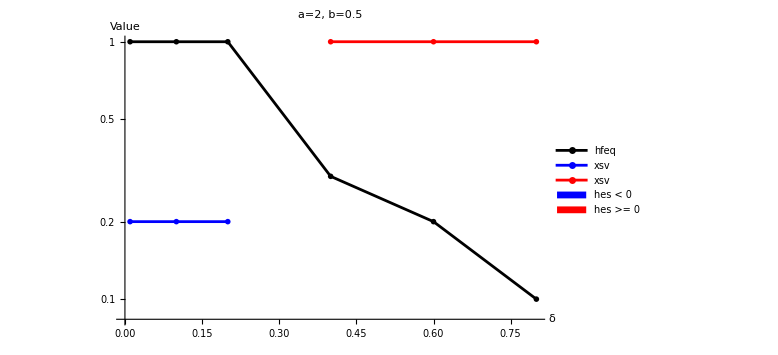

```mathematica
xsv = {};
For[i=1,i<7,i++,xsv = Append[xsv,res2[[i]][[2]][[1]][[2]][[1]]]]
xsv
hfeq = {};
For[i=1,i<7,i++,hfeq = Append[hfeq,res2[[i]][[2]][[1]][[2]][[2]][[1]]]]
hfeq
hes = {}
For[i=1,i<7,i++,hes = Append[hes,Re[res2[[i]][[2]][[1]][[2]][[3]]]]]
hes
colors=If[#<0,Blue,Red]&/@hes;
(*Create separate datasets based on the sign of hes*)
negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=2, b=0.5",18],
GridLines->Automatic,
PlotRange->All,
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

{}

{{0.01,1},{0.1,1},{0.2,1},{0.4,1},{0.6,1},{0.8,1}}

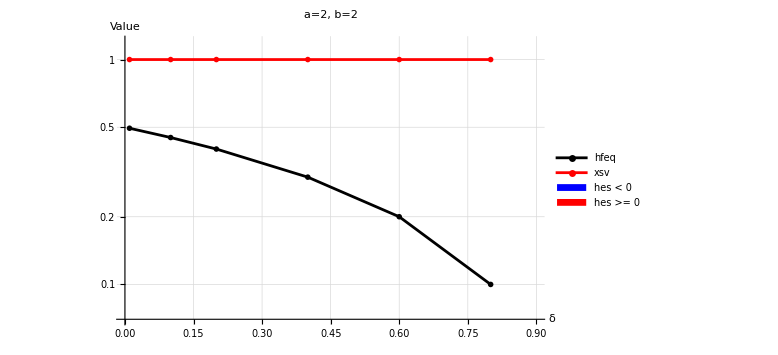

```mathematica
xsv = {};
For[i=1,i<7,i++,xsv = Append[xsv,res3[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<7,i++,hfeq = Append[hfeq,res3[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {};
For[i=1,i<7,i++,hes = Append[hes,Re[res3[[i]][[2]][[1]][[2]][[3]]]]];
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=2, b=2",18],
GridLines->Automatic,
PlotRange->{{0,0.9},{0.07,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotRange->{{0,0.9},{0.07,1.2}},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotRange->{{0,0.9},{0.07,1.2}},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

{}

{{0.01,0.841571},{0.1,0.894151},{0.2,0.96},{0.4,0.995791},{0.6,1}}

{{0.8,1}}

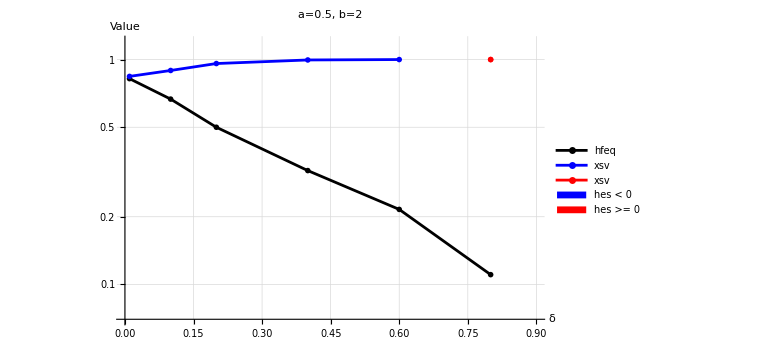

```mathematica
xsv = {};
For[i=1,i<7,i++,xsv = Append[xsv,res4[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<7,i++,hfeq = Append[hfeq,res4[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<7,i++,hes = Append[hes,Re[res4[[i]][[2]][[1]][[2]][[3]]]]];
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=2",18],
GridLines->Automatic,
PlotRange->{{0,0.9},{0.07,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotRange->{{0,0.9},{0.07,1.2}},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotRange->{{0,0.9},{0.07,1.2}},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

{}

{-1.35669,-1.64875,-2.98122,-43.7503,-2.60043,-172.204}

{{0.01,0.75325},{0.1,0.78885},{0.2,0.876701},{0.4,0.991429},{0.6,1},{0.8,1}}

{}

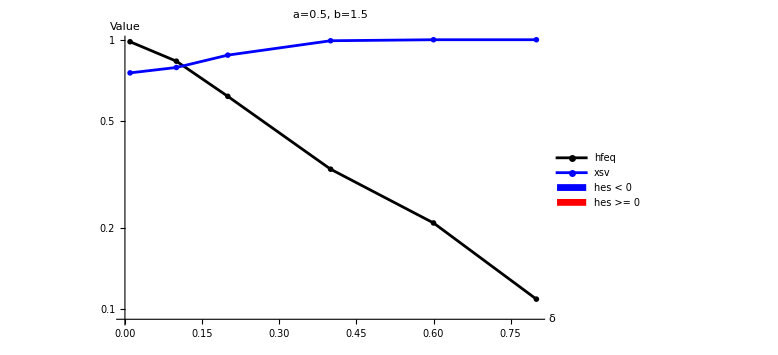

```mathematica
xsv = {};
For[i=1,i<7,i++,xsv = Append[xsv,res42[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<7,i++,hfeq = Append[hfeq,res42[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<7,i++,hes = Append[hes,Re[res42[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=1.5",18],
GridLines->Automatic,
PlotRange->All,
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

```mathematica
testmat = W/.func/.{a->0.5,b->0.5,δ->0.4,s->0,d->0,M0->1,F0->1}/.p->0.001//Simplify//N
```

{{(0.500501 x^0.5 (1.-1. xm)^0.5+(0.0001503+0.500501 (1.-1. x)^0.5) xm^0.5)/((0.001001+1. (1.-1. x)^0.5) x^0.5),0.15015/(0.001001+1. (1.-1. x)^0.5)},{(0.000350701 xm^0.5)/((0.001001+1. (1.-1. x)^0.5) x^0.5),0.35035/(0.001001+1. (1.-1. x)^0.5)}}

```mathematica
testQ = LeadingEigenvaluesAndVectors[Transpose[testmat],1][[2]]
```

{-0.00666667 Re[1/(√x)(350. √x-0.5 (350. √x+√((-350. √x-500. √x √(1.-1. xm)-0.15015 √xm-500. √(1.-1. x) √xm)^2-4. (175000. x √(1.-1. xm)+175000. √(1.-1. x) √x √xm))+500. √x √(1.-1. xm)+0.15015 √xm+500. √(1.-1. x) √xm))],1.}

```mathematica
D[testQ,xm]/.x->0.4/.xm->0.4//Simplify//N
```

{1.0778 Re'[-424.871],0.}

```mathematica
delta = {0.5,0.505,0.51,0.515,0.52,0.54,0.55,0.6};
```

{}

{-0.91125,-0.897269,-0.877762,-0.829906,-3.65674,-5.40456,-6.48137,-15.1905}

{{0.5,0.555555},{0.505,0.567632},{0.51,0.587699},{0.515,0.70337},{0.52,0.963151},{0.54,0.975705},{0.55,0.979915},{0.6,0.991632}}

{}

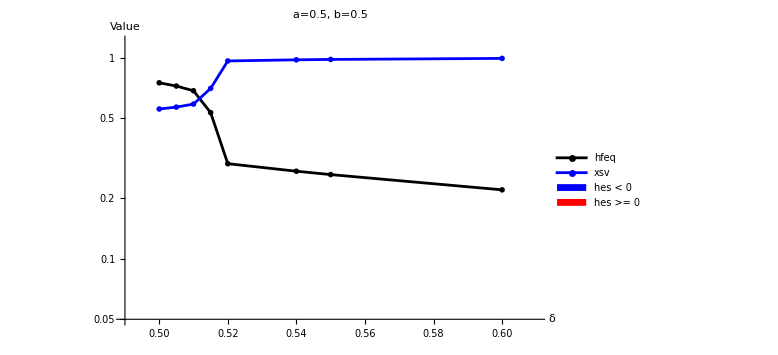

```mathematica
xsv = {};
For[i=1,i<9,i++,xsv = Append[xsv,res12[[i]][[2]][[1]][[2]][[1]]]];

hfeq = {};
For[i=1,i<9,i++,hfeq = Append[hfeq,res12[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<9,i++,hes = Append[hes,Re[res12[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=0.5",18],
GridLines->Automatic,
PlotRange->{{0.49,0.61},{0.05,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotRange->{{0.49,0.61},{0.05,1.2}},PlotMarkers->{"X",20},Joined->True];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotRange->{{0.49,0.61},{0.05,1.2}},PlotMarkers->{"X",20},Joined->True];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

```mathematica
(*s!=0*)
```

```mathematica
res1s4 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->0.5,b->0.5,δ->δval,s->0.5,d->0.2,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
res2s4 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->2,b->0.5,δ->δval,s->0.5,d->0.2,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
res3s4 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->2,b->2,δ->δval,s->0.5,d->0.2,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
res4s4 = Table[{StringForm["δ:``",δval],Table[{StringForm["x initial:``",xval],singvalue1locus[xval,10^-2,10^-9,{a->0.5,b->2,δ->δval,s->0.5,d->0.2,M0->1,F0->1},200,3000]},{xval,{0.1,0.25,0.5,0.9}}]},{δval,{0.01,0.1,0.2,0.4,0.6,0.8,0.999}}];
```

Converged

Converged

Converged

«28 more identical outputs»

x went out of bounds: 1.00353

Converged

Converged

Converged

x went out of bounds: 1.00021

Converged

Converged

Converged

x went out of bounds: 1.00381

x went out of bounds: 1.00199

x went out of bounds: 1.0011

x went out of bounds: 1.00189

x went out of bounds: 1.00064

x went out of bounds: 1.00284

x went out of bounds: 1.00196

x went out of bounds: 1.00311

x went out of bounds: 1.00246

x went out of bounds: 1.00231

x went out of bounds: 1.00146

x went out of bounds: 1.00307

x went out of bounds: 1.00228

x went out of bounds: 1.00337

x went out of bounds: 1.00255

x went out of bounds: 1.0024

x went out of bounds: 1.00061

x went out of bounds: 1.01501

x went out of bounds: 1.00265

x went out of bounds: 1.00572

x went out of bounds: 1.00725

x went out of bounds: 1.00036

x went out of bounds: 1.00337

x went out of bounds: 1.00513

x went out of bounds: 1.008

x went out of bounds: 1.01515

x went out of bounds: 1.00282

x went out of bounds: 1.00256

x went out of bounds: 1.00852

x went out of bounds: 1.0064

x went out of bounds: 1.00931

x went out of bounds: 1.00431

x went out of bounds: 1.00857

x went out of bounds: 1.00442

x went out of bounds: 1.00734

x went out of bounds: 1.01233

x went out of bounds: 1.00737

x went out of bounds: 1.00975

x went out of bounds: 1.01258

x went out of bounds: 1.01288

x went out of bounds: 1.00502

x went out of bounds: 1.00803

x went out of bounds: 1.01065

x went out of bounds: 1.00728

x went out of bounds: 1.00177

Converged

Converged

Converged

«25 more identical outputs»

```mathematica
res1s3
```

{{δ:0.01,{{x initial:0.1,{0.949567,{0.9999,0.0001},-5.22066}},{x initial:0.25,{0.949567,{0.9999,0.0001},-5.22066}},{x initial:0.5,{0.949567,{0.9999,0.0001},-5.22066}},{x initial:0.9,{0.949567,{0.9999,0.0001},-5.22066}}}},{δ:0.1,{{x initial:0.1,{0.949567,{0.9999,0.0001},-5.22065}},{x initial:0.25,{0.949567,{0.9999,0.0001},-5.22065}},{x initial:0.5,{0.949567,{0.9999,0.0001},-5.22065}},{x initial:0.9,{0.949567,{0.9999,0.0001},-5.22065}}}},{δ:0.2,{{x initial:0.1,{0.949567,{0.9999,0.0001},-5.22064}},{x initial:0.25,{0.949567,{0.9999,0.0001},-5.22064}},{x initial:0.5,{0.949567,{0.9999,0.0001},-5.22064}},{x initial:0.9,{0.949567,{0.9999,0.0001},-5.22064}}}},{δ:0.4,{{x initial:0.1,{0.949566,{0.9999,0.0001},-5.22062}},{x initial:0.25,{0.949566,{0.9999,0.0001},-5.22062}},{x initial:0.5,{0.949566,{0.9999,0.0001},-5.22062}},{x initial:0.9,{0.949566,{0.9999,0.0001},-5.22062}}}},{δ:0.6,{{x initial:0.1,{0.949566,{0.9999,0.0001},-5.22059}},{x initial:0.25,{0.949566,{0.9999,0.0001},-5.22059}},{x initial:0.5,{0.949566,{0.9999,0.0001},-5.22059}},{x initial:0.9,{0.949566,{0.9999,0.0001},-5.22059}}}},{δ:0.8,{{x initial:0.1,{0.949566,{0.9999,0.0001},-5.22057}},{x initial:0.25,{0.949566,{0.9999,0.0001},-5.22057}},{x initial:0.5,{0.949566,{0.9999,0.0001},-5.22057}},{x initial:0.9,{0.949566,{0.9999,0.0001},-5.22057}}}},{δ:0.999,{{x initial:0.1,{0.949566,{0.9999,0.0001},-5.22055}},{x initial:0.25,{0.949566,{0.9999,0.0001},-5.22055}},{x initial:0.5,{0.949566,{0.9999,0.0001},-5.22055}},{x initial:0.9,{0.949566,{0.9999,0.0001},-5.22055}}}}}

{}

{-1.24626,-1.24626,-1.24625,-1.24624,-1.24623,-1.24622,-1.33649}

{{0.01,0.722253},{0.1,0.722252},{0.2,0.722251},{0.4,0.72225},{0.6,0.722249},{0.8,0.722247},{0.999,0.754145}}

{}

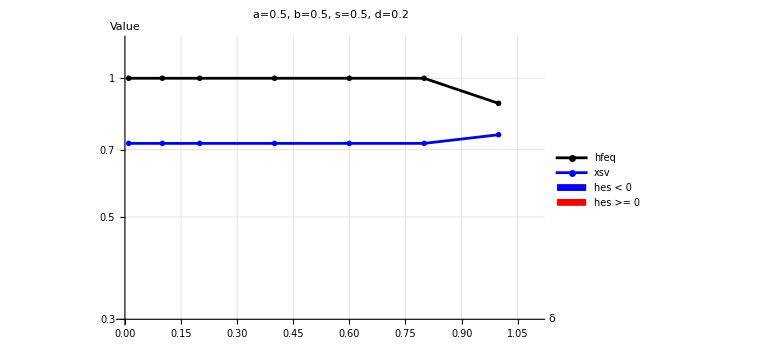

```mathematica
delta = {0.01,0.1,0.2,0.4,0.6,0.8,0.999};
xsv = {};
For[i=1,i<8,i++,xsv = Append[xsv,res1s4[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<8,i++,hfeq = Append[hfeq,res1s4[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<8,i++,hes = Append[hes,Re[res1s4[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=0.5, s=0.5, d=0.2",18],
GridLines->Automatic,
PlotRange->{{0,1.1},{0.3,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

```mathematica
res3s1
```

{{δ:0.01,{{x initial:0.1,{1,{0.497664,0.502336},6.12126}},{x initial:0.25,{1,{0.497644,0.502356},6.10985}},{x initial:0.5,{1,{0.497653,0.502347},6.11736}},{x initial:0.9,{1,{0.497685,0.502315},6.12634}}}},{δ:0.1,{{x initial:0.1,{1,{0.452896,0.547104},7.18205}},{x initial:0.25,{1,{0.452923,0.547077},7.19605}},{x initial:0.5,{1,{0.452907,0.547093},7.18882}},{x initial:0.9,{1,{0.452907,0.547093},7.18885}}}},{δ:0.2,{{x initial:0.1,{1,{0.403142,0.596858},8.98641}},{x initial:0.25,{1,{0.40315,0.59685},9.01075}},{x initial:0.5,{1,{0.403156,0.596844},9.01915}},{x initial:0.9,{1,{0.40316,0.59684},9.02355}}}},{δ:0.4,{{x initial:0.1,{1,{0.303668,0.696332},16.6495}},{x initial:0.25,{1,{0.303683,0.696317},16.7307}},{x initial:0.5,{1,{0.303692,0.696308},16.7599}},{x initial:0.9,{1,{0.303674,0.696326},16.6888}}}},{δ:0.6,{{x initial:0.1,{1,{0.204198,0.795802},40.6489}},{x initial:0.25,{1,{0.20419,0.79581},40.4641}},{x initial:0.5,{1,{0.204199,0.795801},40.6642}},{x initial:0.9,{1,{0.204193,0.795807},40.5467}}}},{δ:0.8,{{x initial:0.1,{1,{0.104714,0.895286},176.093}},{x initial:0.25,{1,{0.104713,0.895287},175.797}},{x initial:0.5,{1,{0.104713,0.895287},175.532}},{x initial:0.9,{1,{0.104714,0.895286},176.046}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.5,Null},{x initial:0.9,Null}}}}

{}

{0.349294,0.349287,0.349279,1.97415,2.82522,6.24972,1567.82}

{}

{{0.01,0.393992},{0.1,0.393991},{0.2,0.393989},{0.4,1},{0.6,1},{0.8,1},{0.999,1}}

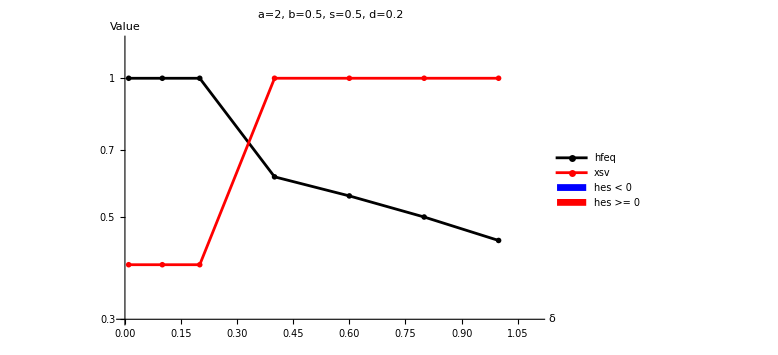

```mathematica
delta =  {0.01,0.1,0.2,0.4,0.6,0.8,0.999};
xsv = {};
For[i=1,i<8,i++,xsv = Append[xsv,res2s4[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<8,i++,hfeq = Append[hfeq,res2s4[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<8,i++,hes = Append[hes,Re[res2s4[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=2, b=0.5, s=0.5, d=0.2",18],
GridLines->Automatic,
PlotRange->{{0,1.1},{0.3,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

```mathematica
res3s1
```

{{δ:0.01,{{x initial:0.1,{1,{0.497664,0.502336},6.12126}},{x initial:0.25,{1,{0.497644,0.502356},6.10985}},{x initial:0.5,{1,{0.497653,0.502347},6.11736}},{x initial:0.9,{1,{0.497685,0.502315},6.12634}}}},{δ:0.1,{{x initial:0.1,{1,{0.452896,0.547104},7.18205}},{x initial:0.25,{1,{0.452923,0.547077},7.19605}},{x initial:0.5,{1,{0.452907,0.547093},7.18882}},{x initial:0.9,{1,{0.452907,0.547093},7.18885}}}},{δ:0.2,{{x initial:0.1,{1,{0.403142,0.596858},8.98641}},{x initial:0.25,{1,{0.40315,0.59685},9.01075}},{x initial:0.5,{1,{0.403156,0.596844},9.01915}},{x initial:0.9,{1,{0.40316,0.59684},9.02355}}}},{δ:0.4,{{x initial:0.1,{1,{0.303668,0.696332},16.6495}},{x initial:0.25,{1,{0.303683,0.696317},16.7307}},{x initial:0.5,{1,{0.303692,0.696308},16.7599}},{x initial:0.9,{1,{0.303674,0.696326},16.6888}}}},{δ:0.6,{{x initial:0.1,{1,{0.204198,0.795802},40.6489}},{x initial:0.25,{1,{0.20419,0.79581},40.4641}},{x initial:0.5,{1,{0.204199,0.795801},40.6642}},{x initial:0.9,{1,{0.204193,0.795807},40.5467}}}},{δ:0.8,{{x initial:0.1,{1,{0.104714,0.895286},176.093}},{x initial:0.25,{1,{0.104713,0.895287},175.797}},{x initial:0.5,{1,{0.104713,0.895287},175.532}},{x initial:0.9,{1,{0.104714,0.895286},176.046}}}},{δ:0.999,{{x initial:0.1,Null},{x initial:0.25,Null},{x initial:0.5,Null},{x initial:0.9,Null}}}}

{}

{9.53291,11.0016,13.138,20.6534,37.7976,94.6362,24746.7}

{}

{{0.01,1},{0.1,1},{0.2,1},{0.4,1},{0.6,1},{0.8,1},{0.999,1}}

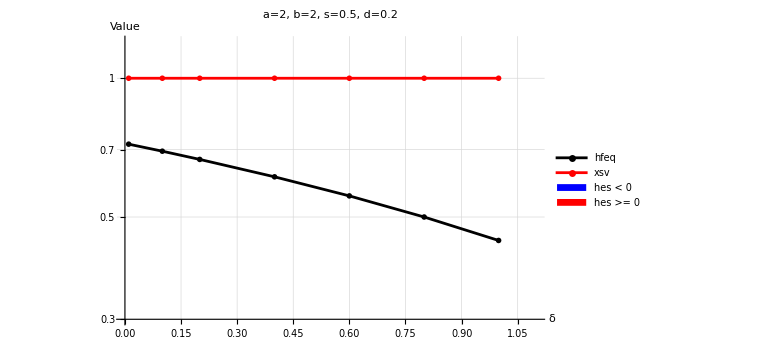

```mathematica
delta = {0.01,0.1,0.2,0.4,0.6,0.8,0.999};
xsv = {};
For[i=1,i<8,i++,xsv = Append[xsv,res3s4[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<8,i++,hfeq = Append[hfeq,res3s4[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<8,i++,hes = Append[hes,Re[res3s4[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=2, b=2, s=0.5, d=0.2",18],
GridLines->Automatic,
PlotRange->{{0,1.1},{0.3,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1},{0.3,1.2}}];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1},{0.3,1.2}}];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

{}

{-7.29178,-7.94946,-10.2686,-17.3313,-30.2784,-55.4807,-107.255}

{{0.01,0.912302},{0.1,0.918034},{0.2,0.933431},{0.4,0.957962},{0.6,0.975373},{0.8,0.986722},{0.999,0.993379}}

{}

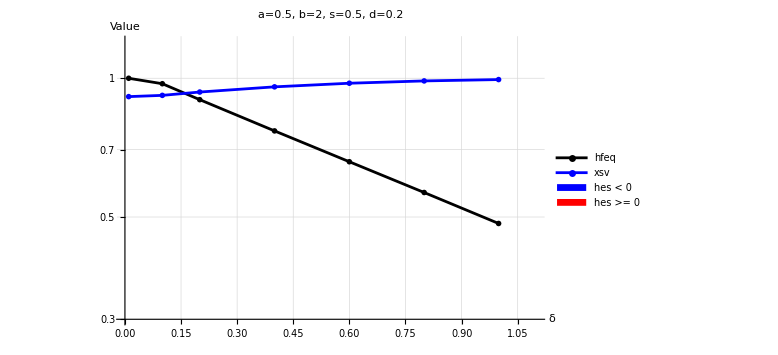

```mathematica
delta = {0.01,0.1,0.2,0.4,0.6,0.8,0.999};
xsv = {};
For[i=1,i<8,i++,xsv = Append[xsv,res4s4[[i]][[2]][[1]][[2]][[1]]]];
hfeq = {};
For[i=1,i<8,i++,hfeq = Append[hfeq,res4s4[[i]][[2]][[1]][[2]][[2]][[1]]]];
hes = {}
For[i=1,i<8,i++,hes = Append[hes,Re[res4s4[[i]][[2]][[1]][[2]][[3]]]]];
hes
colors=If[#<0,Blue,Red]&/@hes;
 negativePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Blue&][[All,{1,2}]]
positivePoints=Select[Transpose[{delta,xsv,colors}],#[[3]]==Red&][[All,{1,2}]]
 mainplot = ListLogPlot[
{
Transpose[{delta,hfeq}]
},
Joined->True,(*Connect the points with a line*)
PlotStyle->{Black},
PlotMarkers->{{"o",20}},
PlotLegends->{"hfeq"},
AxesLabel->{"δ","Value"},
PlotLabel->Style["a=0.5, b=2, s=0.5, d=0.2",18],
GridLines->Automatic,
PlotRange->{{0,1.1},{0.3,1.2}},
LabelStyle->Directive[Black,16],
TicksStyle->Directive[Black,14],
ImageSize->Large
];
negativePointsPlot=ListLogPlot[negativePoints,PlotStyle->Blue,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
positivePointsPlot=ListLogPlot[positivePoints,PlotStyle->Red,PlotLegends->{"xsv"},PlotMarkers->{"X",20},Joined->True,PlotRange->{{0,1.1},{0.3,1.2}}];
customLegend=SwatchLegend[{Blue,Red},{"hes < 0","hes >= 0"},LegendMarkerSize->{24,12},LegendLabel->"Sign of hessian"];
Legended[Show[mainplot,negativePointsPlot,positivePointsPlot],customLegend]
```

```mathematica
Table[singvalue1locus[x,0.01,10^-6,{a->0.5,b->0.5,δ->0.5,s->0,d->0,M0->1,F0->1},200,500],{x,{0.25,0.5,0.75,0.4}}]
```

Converged

Converged

Converged

«1 more identical outputs»

{{0.499952,{1.,1.01696×10^-13}},{0.522117,{0.853553,0.146447}},{0.75,{0.5,0.5}},{0.499964,{0.999859,0.000141212}}}

```mathematica
results
```

{{0.499932,{2.22045×10^-16,1.}},{0.5,{2.22045×10^-16,1.}},{0.50081,{3.33067×10^-16,1.}}}

```mathematica
res
```

0.500566

```mathematica
Print[npar];
```

{a→0.5,b→0.5,δ→0,s→0,d→0,M0→1,F0→1}

```mathematica
10^-3
```

1/1000

False

```mathematica
(*Define the number of grid points per dimension*)
numGridPoints=4; (*For example,20 points will give you 400 combinations*)

(*Generate the grid points*)
aValues=bValues=N[Range[0.05,0.95,(0.95-0.05)/(numGridPoints-1)]];

(*Generate the parameter sets*)
nparValues=Flatten[Table[{a->aVal,b->bVal,δ->0,s->0,d->0,M0->1,F0->1},{aVal,aValues},{bVal,bValues}],1];

(*Function to run singvalue1locus and collect results*)
runSimulations[nparValues_,initialXVals_,eps_,tol_,gensValue_,maxIterval_]:=
Table[
{nparRule,
Table[
singvalue1locus[x,eps,tol,nparRule,gensValue,maxIterval],
{x,initialXVals}
]
},
{nparRule,nparValues}
];


(*Initial x values*)
initialXVals={0.25,0.5,0.75};
```

```mathematica
nparValues
```

{{a→0.05,b→0.05,δ→0,s→0,d→0,M0→1,F0→1},{a→0.05,b→0.95,δ→0,s→0,d→0,M0→1,F0→1},{a→0.95,b→0.05,δ→0,s→0,d→0,M0→1,F0→1},{a→0.95,b→0.95,δ→0,s→0,d→0,M0→1,F0→1}}

```mathematica
npar
```

{a→0.95,b→0.65,δ→0,s→0,d→0,M0→1,F0→1}

```mathematica
npar = {a->0.95,b->0.65,δ->0,s->0,d->0,M0->1,F0->1}
```

{a→0.95,b→0.65,δ→0,s→0,d→0,M0→1,F0→1}

```mathematica
npar
```

{a→0.95,b→0.65,δ→0,s→0,d→0,M0→1,F0→1}

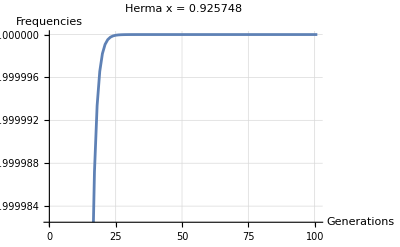

Maximum iterations reached without convergence.

{0.931899,{0.01,0.99}}

```mathematica
singvalue1locus[0.05,0.01,10^-6,{a->0.05,b->0.95,δ->0,s->0,d->0,M0->1,F0->1},100,100]
```

```mathematica
nparRule
```

nparRule